```mathematica
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
```

```mathematica
DFTC[list_,rev_]:=Module[{numItems,i,k,j,returnList,intensity},
returnList={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
];

For[k=1,k<=numItems,k++,
intensity=list[[k]];
For [i=0,i<numItems/2,i++,
If[i==0 ||i==(numItems/2-1),
returnList[[i+1]]=returnList[[i+1]]+1/numItems*intensity*Cos[2*π *i *rev* (k-1)/numItems];,
returnList[[i+1]]=returnList[[i+1]]+2/numItems*intensity*Cos[2*π *i* rev *(k-1)/numItems];
];
];
];

returnList
];
DFTS[list_,rev_]:=Module[{numItems,i,k,j,returnList,intensity},
returnList={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
];

For[k=1,k<=numItems,k++,
intensity=list[[k]];
For [i=0,i<numItems/2,i++,
If[i==0 ||i==(numItems/2-1),
returnList[[i+1]]=returnList[[i+1]]+1/numItems*intensity*Sin[2*π *i *rev* (k-1)/numItems];,
returnList[[i+1]]=returnList[[i+1]]+2/numItems*intensity*Sin[2*π *i* rev *(k-1)/numItems];
];
];
];

returnList
];
DFT[list_,rev_]:={DFTS[list,rev],DFTC[list,rev]};
```

```mathematica
folder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox","00School","Research","DataRuns","17-09-20"}];
folder=FileNameJoin[{"Z:","RbData","2017-09-21"}];
SetDirectory[folder];
FileNames[]
data=Import["lpDataCSV.csv","csv"];
data=Take[data,{1,-2},All];
angle=Transpose[data][[1]];
intensityArray=Transpose[data][[2]];
angleRAD=angle*π/180;

fc=DFT[intensityArray,1] (*fc=fourier coefficients*)
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
```

{FDayRotation2017-09-21_122352.dat,FDayRotation2017-09-21_122352.png,FDayRotation2017-09-21_122352RotationAnalysis.dat,FDayRotation2017-09-21_122454.dat,FDayRotation2017-09-21_122454.png,FDayRotation2017-09-21_122454RotationAnalysis.dat,FDayRotation2017-09-21_122549.dat,FDayRotation2017-09-21_122549.png,FDayRotation2017-09-21_122549RotationAnalysis.dat,FDayRotation2017-09-21_122957.dat,FDayRotation2017-09-21_122957.png,FDayRotation2017-09-21_122957RotationAnalysis.dat,FDayRotation2017-09-21_123041.dat,FDayRotation2017-09-21_123041.png,FDayRotation2017-09-21_123041RotationAnalysis.dat,FDayRotation2017-09-21_123120.dat,FDayRotation2017-09-21_123120.png,FDayRotation2017-09-21_123120RotationAnalysis.dat,FDayRotation2017-09-21_134635.dat,FDayRotation2017-09-21_134635.png,FDayRotation2017-09-21_134635RotationAnalysis.dat,FDayRotation2017-09-21_134824.dat,FDayRotation2017-09-21_134824.png,FDayRotation2017-09-21_134824RotationAnalysis.dat,FDayRotation2017-09-21_134925.dat,FDayRotation2017-09-21_134925.png,FDayRotation2017-09-21_134925RotationAnalysis.dat,FDayRotation2017-09-21_134949.dat,FDayRotation2017-09-21_134949.png,FDayRotation2017-09-21_134949RotationAnalysis.dat,FDayRotation2017-09-21_135013.dat,FDayRotation2017-09-21_135013.png,FDayRotation2017-09-21_135013RotationAnalysis.dat,FDayRotation2017-09-21_135231.dat,FDayRotation2017-09-21_135231.png,FDayRotation2017-09-21_135231RotationAnalysis.dat,FDayRotation2017-09-21_135352.dat,FDayRotation2017-09-21_135352.png,FDayRotation2017-09-21_135352RotationAnalysis.dat,FDayRotation2017-09-21_135458.dat,FDayRotation2017-09-21_135458.png,FDayRotation2017-09-21_135458RotationAnalysis.dat,FDayRotation2017-09-21_135552.dat,FDayRotation2017-09-21_135552.png,FDayRotation2017-09-21_135552RotationAnalysis.dat,FDayRotation2017-09-21_135712.dat,FDayRotation2017-09-21_135712.png,FDayRotation2017-09-21_135712RotationAnalysis.dat,FDayRotation2017-09-21_135814.dat,FDayRotation2017-09-21_135814.png,FDayRotation2017-09-21_135814RotationAnalysis.dat,FDayRotation2017-09-21_135913.dat,FDayRotation2017-09-21_135913.png,FDayRotation2017-09-21_135913RotationAnalysis.dat,FDayRotation2017-09-21_140015.dat,FDayRotation2017-09-21_140015.png,FDayRotation2017-09-21_140015RotationAnalysis.dat,FDayRotation2017-09-21_140114.dat,FDayRotation2017-09-21_140114.png,FDayRotation2017-09-21_140114RotationAnalysis.dat,FDayRotation2017-09-21_140229.dat,FDayRotation2017-09-21_140229.png,FDayRotation2017-09-21_140229RotationAnalysis.dat,FDayRotation2017-09-21_140733.dat,FDayRotation2017-09-21_140733.png,FDayRotation2017-09-21_140733RotationAnalysis.dat,FDayRotation2017-09-21_140842.dat,FDayRotation2017-09-21_140842.png,FDayRotation2017-09-21_140842RotationAnalysis.dat,FDayRotation2017-09-21_141734.dat,FDayRotation2017-09-21_141734.png,FDayRotation2017-09-21_141734RotationAnalysis.dat,FDayRotation2017-09-21_141844.dat,FDayRotation2017-09-21_141844.png,FDayRotation2017-09-21_141844RotationAnalysis.dat,FDayRotation2017-09-21_141952.dat,FDayRotation2017-09-21_141952.png,FDayRotation2017-09-21_141952RotationAnalysis.dat,FDayRotation2017-09-21.dat}

Import::nffil: File not found during Import.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,-2},All].

Part::partw: Part 2 of Transpose[Take[$Failed,{1,-2},All]] does not exist.

{{0},{1+1/2 Transpose[Take[$Failed,{1,-2},All]]}}

Part::partw: Part 3 of {1+1/2 Transpose[Take[$Failed,{1,-2},All]]} does not exist.

Part::partw: Part 3 of {0} does not exist.

(√(({0}⟦3⟧)^2+({1+1/2 Transpose[Take[$Failed,{1,-2},All]]}⟦3⟧)^2))/(1+1/2 Transpose[Take[$Failed,{1,-2},All]])

```mathematica
folder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox","00School","Research","DataRuns","17-09-20"}];
```

```mathematica
GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];
```

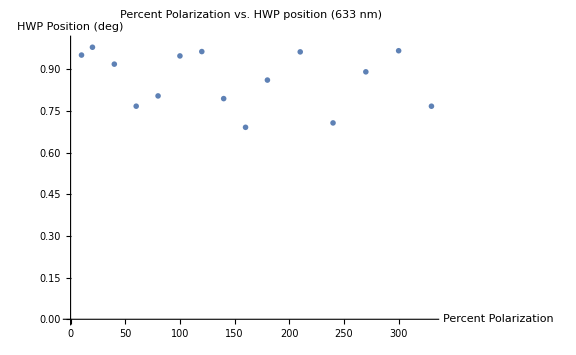

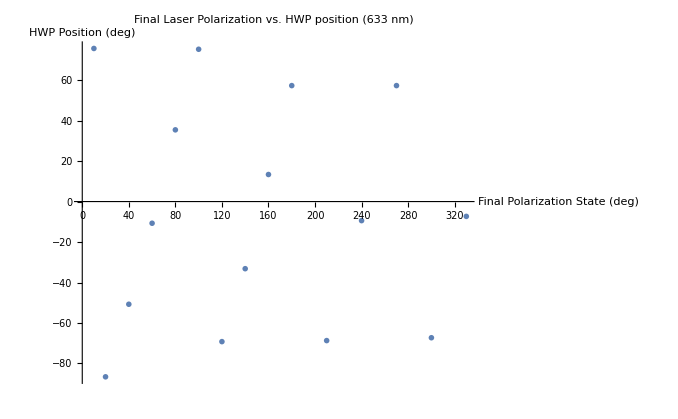

```mathematica
hwpAngles={10,20,40,60,80,100,120,140,160,180,210,240,270,300,330};
percentPol={.9520,.9802,.9193,.7678,.8048,.9489,.9646,.7951,.6917,.8619,.9635,.7075,.8916,.9676,.7677};
laserPolarizationAngle={75.65,-86.60,-50.74,-10.71,35.44,75.26,-69.21,-33.17,13.37,57.30,-68.70,-9.42,57.30,-67.29,-7.32};
plotTitle="Percent Polarization vs. HWP position (633 nm)";
yAxisTitle="Percent Polarization";
xAxisTitle="HWP Position (deg)";
ListPlot[Transpose[{hwpAngles,percentPol}],PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotRange->{0,1},PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]

plotTitle="Final Laser Polarization vs. HWP position (633 nm)";
yAxisTitle="Final Polarization State (deg)";
xAxisTitle="HWP Position (deg)";
ListPlot[Transpose[{hwpAngles,laserPolarizationAngle}],PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]
```

```mathematica
GetLinearPolarizationFraction[{"FDayRotation2017-09-21_135231.dat","FDayRotation2017-09-21_135352.dat"}]
GetAngle["FDayRotation2017-09-21_135231.dat"]*180/π/2
fileNames=GenerateListOfFileNames["FDayRotation","2017-09-21",{"135231","135352"}]
GetLinearPolarizationFraction[fileNames]
```

{0.951966,0.980163}

0.11699   -0.213695

75.6504

{FDayRotation2017-09-21_135231.dat,FDayRotation2017-09-21_135352.dat}

{0.951966,0.980163}

```mathematica
times={141844,141952};
names=GenerateListOfFileNames["FDayRotation","2017-09-21",times];
GetLinearPolarizationFraction[names]
GetAngle[names]*180/π
```

{0.967642,0.767682}

{-67.2893,-7.31775}